## Metricas del fluido perfecto e indice del politropo

```mathematica
ξ[r_]:=Log[(A-(B)*(r^2))^2];
μ[r_]:=-Log[1+(c)(r^2)((A)-3(r^2)(B))^(-2/3)];
Γ:=1+1/n
```

## Ecuación diferencial master para la obtención de la deformación del espacio f

```mathematica
DSolve[f'[r]/r+f[r]/r^2==-(Ka)^(Γ)(1/r^2-Exp[-μ[r]](1/r^2-μ'[r]/r)),f[r],r]
```

{{f[r]→(c Ka^(1+1/n) r^2)/((A-3 B r^2)^(2/3))+C[1]/r}}

```mathematica
f[r_]:=(c Ka^(1+1/n) r^2)/((A-3 B r^2)^(2/3))
```

## Ecuación diferencial para la obtención de la derivada de la deformación del tiempo

```mathematica
gprime[r_]:=(r/(Exp[-μ[r]]+f[r]))(κ Ka((Ka)^(Γ)/κ(1/r^2-Exp[-μ[r]](1/r^2-μ'[r]/r)))^(Γ) -f[r](1/r^2+ξ'[r]/r))
```

```mathematica
gprime[r]//FullSimplify
```

(r (-(c Ka^(1+1/n) (A-5 B r^2))/((A-3 B r^2)^(2/3) (A-B r^2))+Ka (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))/(1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3)))

```mathematica
gprime[r_]:=(r (-(c Ka^(1+1/n) (A-5 B r^2))/((A-3 B r^2)^(2/3) (A-B r^2))+Ka (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))/(1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3)));
```

```mathematica
gprime[r]/.{M->u R,r->x R}//FullSimplify
```

(x (4.95325×10^-6 (((-0.9-4.76213 √(1-2. u))^(2/3) u (1.35-14.2864 √(1-2. u)-2.25 x^2))/((0.45-4.76213 √(1-2. u)-1.35 x^2)^(5/3)))^3.+((-0.9-4.76213 √(1-2. u))^(2/3) u (-0.017776+0.188115 √(1-2. u)+0.0888802 x^2))/((0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3) (-0.0944955+1. √(1-2. u)+0.0944955 x^2))))/(1-(2. (-0.9-4.76213 √(1-2. u))^(2/3) u x^2)/((0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3)))

```mathematica
gprimeg[x_]:=(x (4.953253211044616*^-6 (((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (1.3499999999999999-14.286394828777734 √(1-2. u)-2.25 x^2))/(0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(5/3))^3.+((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (-0.017776049480171672+0.1881153047182383 √(1-2. u)+0.08888024740085836 x^2))/((0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3) (-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 x^2))))/(1-(2. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u x^2)/((0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3)))
```

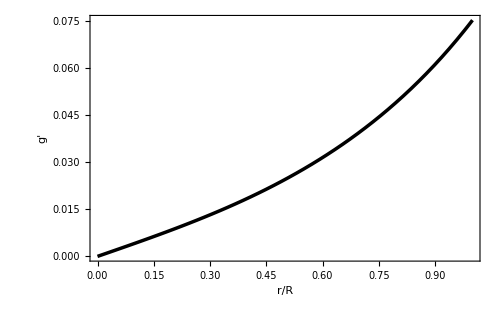

```mathematica
solu1:=Re[gprimeg[x]]/.{u->0.17642618727114115}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","g'"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

## Cambio en la geometria del espacio-tiempo

### Derivada de ν, para el tiempo

```mathematica
νprime[r_]:=D[ξ[r],r]+gprime[r]
νprime[r]//FullSimplify
```

-(4 B r)/(A-B r^2)+(r (-(c Ka^(1+1/n) (A-5 B r^2))/((A-3 B r^2)^(2/3) (A-B r^2))+Ka (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))/(1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3)))

```mathematica
νprime[r_]:=-(4 B r)/(A-B r^2)+(r (-(c Ka^(1+1/n) (A-5 B r^2))/((A-3 B r^2)^(2/3) (A-B r^2))+Ka (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))/(1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3)));
```

### Cambio de λ, para el espacio

```mathematica
λ[r_]:=-Log[Exp[-μ[r]]+f[r]]
```

```mathematica
λ[r]//FullSimplify
```

-Log[1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3))]

```mathematica
λ[r_]:=-Log[1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3))];
```

## Ecuaciones de Einstein

### Densidad Efectiva

```mathematica
ρ[r_]:=1/(κ r^2)(1-ⅇ^(-λ[r])(1-r D[λ[r],r]));
ρ[r]//FullSimplify
```

-(c (1+Ka^(1+1/n)) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ)

```mathematica
ρ[r_]:=-(c (1+Ka^(1+1/n)) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ);
```

### Presión efectiva

```mathematica
Pr[r_]:=-1/(κ r^2)(1-ⅇ^(-λ[r])(1+r *νprime[r]));
Pr[r]//FullSimplify
```

1/((A-3 B r^2) (A-B r^2) κ)(-4 A B+12 B^2 r^2+c (A-5 B r^2) (A-3 B r^2)^(1/3)+Ka (A-3 B r^2) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)

```mathematica
Pr[r_]:=1/((A-3 B r^2) (A-B r^2) κ)(-4 A B+12 B^2 r^2+c (A-5 B r^2) (A-3 B r^2)^(1/3)+Ka (A-3 B r^2) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)
```

### Presión Tangencial efectiva

```mathematica
Pt[r_]:=Exp[-λ[r]]/(4κ)(2νprime'[r]+(νprime[r])^2-λ'[r]νprime[r]+(2(νprime[r]-λ'[r]))/r);
Pt[r]//Simplify
```

((1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3))) (-2 c (1+Ka^(1+1/n)) n r^3 (A-3 B r^2) (A-B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)+4 B (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)+n r^3 (A-3 B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)+4 B (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)^2-2 n (A-3 B r^2) (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (-2 c (1+Ka^(1+1/n)) r (A-B r^2)^2+4 B r (A-3 B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))+r (A-3 B r^2) (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))-2 r (8 B^2 n r^2 (A-3 B r^2)^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2+4 B n (A-3 B r^2)^2 (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2+2 B c Ka^(1+1/n) r^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (n (A-5 B r^2) (A-3 B r^2)^2+2 n (A-5 B r^2) (A-3 B r^2) (A-B r^2)-5 n (A-3 B r^2)^2 (A-B r^2)+10 Ka (1+n) (A-B r^2)^3 (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1/n))-2 c (1+Ka^(1+1/n)) n r^2 (A-3 B r^2) (A-B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)+n (A-3 B r^2)^2 (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))))/(4 n r (A-3 B r^2)^2 (A-B r^2)^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2 κ)

```mathematica
Pt[r_]:=((1+(c (1+Ka^(1+1/n)) r^2)/((A-3 B r^2)^(2/3))) (-2 c (1+Ka^(1+1/n)) n r^3 (A-3 B r^2) (A-B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)+4 B (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)+n r^3 (A-3 B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)+4 B (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)^2-2 n (A-3 B r^2) (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (-2 c (1+Ka^(1+1/n)) r (A-B r^2)^2+4 B r (A-3 B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))+r (A-3 B r^2) (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))-2 r (8 B^2 n r^2 (A-3 B r^2)^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2+4 B n (A-3 B r^2)^2 (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2+2 B c Ka^(1+1/n) r^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (n (A-5 B r^2) (A-3 B r^2)^2+2 n (A-5 B r^2) (A-3 B r^2) (A-B r^2)-5 n (A-3 B r^2)^2 (A-B r^2)+10 Ka (1+n) (A-B r^2)^3 (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1/n))-2 c (1+Ka^(1+1/n)) n r^2 (A-3 B r^2) (A-B r^2)^2 (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ)+n (A-3 B r^2)^2 (A-B r^2) (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3)) (c Ka^(1+1/n) (A-5 B r^2)-Ka (A-3 B r^2)^(2/3) (A-B r^2) (-(c Ka^(1+1/n) (3 A-5 B r^2))/((A-3 B r^2)^(5/3) κ))^(1+1/n) κ))))/(4 n r (A-3 B r^2)^2 (A-B r^2)^2 (c (1+Ka^(1+1/n)) r^2+(A-3 B r^2)^(2/3))^2 κ)
```

## Resolución de la integral numérica de gprima, mediante MATLAB

```mathematica
gnume:=-3.121390770288911
```

```mathematica
νnumer[r_]:=ξ[r]+gnume
```

## Aplicación de las condiciones de frontera

```mathematica
Solve[Exp[-λ[R]]==1-(2M)/R,c]
```

{{c→-(2 M (A-3 B R^2)^(2/3))/((1+Ka^(1+1/n)) R^3)}}

```mathematica
c:=-(2 M (A-3 B R^2)^(2/3))/((1+Ka^(1+1/n)) R^3)
```

```mathematica
NSolve[Exp[νnumer[R]]==1-(2M)/R,A]
```

{{A→3.21563×10^-7 (3.10981×10^6 B R^2-(1.48093×10^7 √(-2. M+R))/(√R))},{A→3.21563×10^-7 (3.10981×10^6 B R^2+(1.48093×10^7 √(-2. M+R))/(√R))}}

```mathematica
A:=3.2156295028861884*^-7 (3.109811*^6 B R^2-(1.4809329262958705*^7 √(-2. M+R))/(√R))
```

### Damos las constantes que usamos en la integración

```mathematica
B=0.45;
Ka=0.47;
n=0.5;
κ=8*π;
R=1;
```

```mathematica
Clear[A,B,c,Ka,n,κ,R]
```

## Intercambio Energético

```mathematica
DEnergy[r_]:=gprime[r]/(2κ)×Exp[-μ[r]]/r(ξ'[r]+μ'[r])
DEnergy[r]/.{M->u R,r->x R}//FullSimplify
```

-((1.50655×10^-9 x ((0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3) (((-0.9-4.76213 √(1-2. u))^(2/3) u (-0.283486+3. √(1-2. u)+0.472477 x^2))/((0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3) (-0.0944955+1. √(1-2. u)+0.283486 x^2)))^3. (-1.+10.5825 √(1-2. u)+1. x^2)+(-0.9-4.76213 √(1-2. u))^(2/3) u (-37978.1+401904. √(1-2. u)+189891. x^2)) (44.7958 (-0.9-4.76213 √(1-2. u))^(2/3) u^2+(0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3) (0.220765-2.33624 √(1-2. u)-0.662294 x^2)+(-0.9-4.76213 √(1-2. u))^(2/3) u (-22.5979+4.23301 √(1-2. u)-1.04435×10^-15 √(1-2. u) x^2+1. x^4)))/((0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3) (0.0944955-1. √(1-2. u)-0.0944955 x^2)^2 (-0.0944955+1. √(1-2. u)+0.283486 x^2) (-2. (-0.9-4.76213 √(1-2. u))^(2/3) u x^2+1. (0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3))))

```mathematica
DEnergy[x_]:=-((1.5065536126488855*^-9 x ((0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3) (((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (-0.2834864952662446+3. √(1-2. u)+0.4724774921104076 x^2))/((0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3) (-0.09449549842208152+1. √(1-2. u)+0.2834864952662446 x^2)))^3. (-1.+10.582514687983506 √(1-2. u)+1. x^2)+(-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (-37978.13208878246+401904.14065171813 √(1-2. u)+189890.66044391232 x^2)) (44.79584684855467 (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u^2+(0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3) (0.22076460000000006-2.3362446220868036 √(1-2. u)-0.6622938 x^2)+(-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (-22.59792342427733+4.233005875193405 √(1-2. u)-1.0443512413362841*^-15 √(1-2. u) x^2+1. x^4)))/((0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3) (0.09449549842208152-1. √(1-2. u)-0.09449549842208152 x^2)^2 (-0.09449549842208152+1. √(1-2. u)+0.2834864952662446 x^2) (-2. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u x^2+1. (0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3))))
```

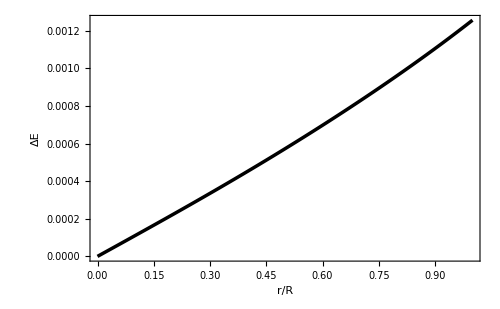

```mathematica
solu1:=Re[DEnergy[x]]/.{u->0.17642618727114115}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ΔE"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
DEnergy[x]/.{x->√(x^2+y^2)}//FullSimplify
```

-((1.50655×10^-9 √(x^2+y^2) ((0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (((-0.9-4.76213 √(1-2. u))^(2/3) u (-0.283486+3. √(1-2. u)+0.472477 (x^2+y^2)))/((0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.0944955+1. √(1-2. u)+0.283486 (x^2+y^2))))^3. (-1.+10.5825 √(1-2. u)+1. (x^2+y^2))+(-0.9-4.76213 √(1-2. u))^(2/3) u (-37978.1+401904. √(1-2. u)+189891. (x^2+y^2))) (44.7958 (-0.9-4.76213 √(1-2. u))^(2/3) u^2+(0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (0.220765-2.33624 √(1-2. u)-0.662294 (x^2+y^2))+(-0.9-4.76213 √(1-2. u))^(2/3) u (-22.5979+4.23301 √(1-2. u)-1.04435×10^-15 √(1-2. u) (x^2+y^2)+1. (x^2+y^2)^2)))/((0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (0.0944955-1. √(1-2. u)-0.0944955 (x^2+y^2))^2 (-0.0944955+1. √(1-2. u)+0.283486 (x^2+y^2)) (-2. (-0.9-4.76213 √(1-2. u))^(2/3) u (x^2+y^2)+1. (0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(2/3))))

```mathematica
dEnergy[x_,y_]:=-((1.5065536126488855*^-9 √(x^2+y^2) ((0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (-0.2834864952662446+3. √(1-2. u)+0.4724774921104076 (x^2+y^2)))/((0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.09449549842208152+1. √(1-2. u)+0.2834864952662446 (x^2+y^2))))^3. (-1.+10.582514687983506 √(1-2. u)+1. (x^2+y^2))+(-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (-37978.13208878246+401904.14065171813 √(1-2. u)+189890.66044391232 (x^2+y^2))) (44.79584684855467 (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u^2+(0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (0.22076460000000006-2.3362446220868036 √(1-2. u)-0.6622938 (x^2+y^2))+(-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (-22.59792342427733+4.233005875193405 √(1-2. u)-1.0443512413362841*^-15 √(1-2. u) (x^2+y^2)+1. (x^2+y^2)^2)))/((0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (0.09449549842208152-1. √(1-2. u)-0.09449549842208152 (x^2+y^2))^2 (-0.09449549842208152+1. √(1-2. u)+0.2834864952662446 (x^2+y^2)) (-2. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (x^2+y^2)+1. (0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(2/3))))
```

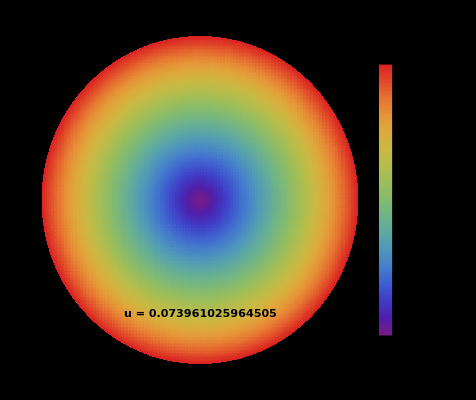

```mathematica
DensityPlot[Re[dEnergy[x,y]]/.{u->0.17642618727114115},{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},0<x^2+y^2<1],ColorFunction->"Rainbow",MeshStyle->Opacity[0.1,Black],PlotLegends->Automatic,Background->Black,Frame->False,Epilog->Text[Style["u = 0.173961025964505",Large,Bold],{0,-0.7}],PlotPoints->100]
```

## Condiciones de aceptabilidad

### Sector material

```mathematica
ρ[r]//FullSimplify
```

(0.0795775 (-0.9-4.76213 √(1-2. M))^(2/3) M (1.35-14.2864 √(1-2. M)-2.25 r^2))/((0.45-4.76213 √(1-2. M)-1.35 r^2)^(5/3))

```mathematica
Pr[r]/.{M-> u R, r->x R}//FullSimplify
```

(0.00175452 (-0.81+8.57184 √(1-2. u)+2.43 x^2+0.000112329 (((-0.9-4.76213 √(1-2. u))^(2/3) u (1.35-14.2864 √(1-2. u)-2.25 x^2))/((0.45-4.76213 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.0944955+1. √(1-2. u)+0.0944955 x^2) (-0.0944955+1. √(1-2. u)+0.283486 x^2)+(-0.9-4.76213 √(1-2. u))^(2/3) u (0.45-4.76213 √(1-2. u)-1.35 x^2)^(1/3) (-0.815348+8.62843 √(1-2. u)+4.07674 x^2)))/((-0.0944955+1. √(1-2. u)+0.0944955 x^2) (-0.0944955+1. √(1-2. u)+0.283486 x^2))

```mathematica
Prg[x_]:=(0.0017545160802817416 (-0.81+8.571836897266643 √(1-2. u)+2.43 x^2+0.00011232936844855853 (((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (1.3499999999999999-14.286394828777734 √(1-2. u)-2.25 x^2))/(0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 x^2) (-0.09449549842208152+1. √(1-2. u)+0.2834864952662446 x^2)+(-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(1/3) (-0.8153481128767929+8.628433380338295 √(1-2. u)+4.0767405643839645 x^2)))/((-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 x^2) (-0.09449549842208152+1. √(1-2. u)+0.2834864952662446 x^2))
```

```mathematica
Solve[Prg[1]==0,u]
```

{{u→-119.251},{u→0.176426},{u→0.499204},{u→116.426-2.88206 ⅈ},{u→116.426+2.88206 ⅈ}}

```mathematica
Prg[1]/.u->0.17642618727114115
```

1.55992×10^-17

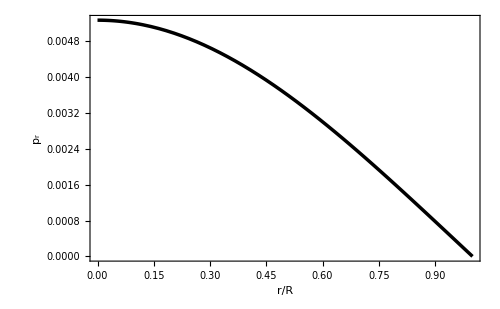

```mathematica
solu1:=Re[Prg[x]]/.{u->0.17642618727114115}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","p_r"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Full]
```

```mathematica
Pt[r]/.{M-> u R, r->x R}//Simplify
```

(9.67085×10^-6 (1-(2. (-0.9-4.76213 √(1-2. u))^(2/3) u x^2)/((0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3))) (-146.953 x^2 (0.0944955-1. √(1-2. u)-0.283486 x^2)^2 (1. (-0.9-4.76213 √(1-2. u))^(2/3) u x^2-0.5 (0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3))^2+777.565 (0.0944955-1. √(1-2. u)-0.283486 x^2)^2 (-0.0944955+1. √(1-2. u)+0.0944955 x^2) (1. (-0.9-4.76213 √(1-2. u))^(2/3) u x^2-0.5 (0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3))^2+0.338608 (-0.9-4.76213 √(1-2. u))^(2/3) u x^2 (-2. (-0.9-4.76213 √(1-2. u))^(2/3) u x^2+(0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3)) (-107.995 (-0.0944955+1. √(1-2. u))^3-91.8455 (0.0944955-1. √(1-2. u))^2 x^2-22.1796 (-0.0944955+1. √(1-2. u)) x^4-1.36688 x^6+215.99 (-0.0944955+1. √(1-2. u)) (0.0944955-1. √(1-2. u)-0.283486 x^2)^2-0.0426542 (((-0.9-4.76213 √(1-2. u))^(2/3) u (1.35-14.2864 √(1-2. u)-2.25 x^2))/((0.45-4.76213 √(1-2. u)-1.35 x^2)^(5/3)))^2. (-0.0944955+1. √(1-2. u)+0.0944955 x^2)^3)+0.5 x^2 (0.45-4.76213 √(1-2. u)-1.35 x^2)^2 (3.6 (-0.9-4.76213 √(1-2. u))^(2/3) u x^2-1.8 (0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3)-0.000023588 (((-0.9-4.76213 √(1-2. u))^(2/3) u (1.35-14.2864 √(1-2. u)-2.25 x^2))/((0.45-4.76213 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3) (-0.0944955+1. √(1-2. u)+0.0944955 x^2)-0.89583 (-0.9-4.76213 √(1-2. u))^(2/3) u (-0.0944955+1. √(1-2. u)+0.472477 x^2))^2-4. (-0.9-4.76213 √(1-2. u))^(2/3) u x^2 (0.45-4.76213 √(1-2. u)-1.35 x^2) (0.45-4.76213 √(1-2. u)-0.45 x^2)^2 (0.000023588 (((-0.9-4.76213 √(1-2. u))^(2/3) u (1.35-14.2864 √(1-2. u)-2.25 x^2))/((0.45-4.76213 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3) (-0.0944955+1. √(1-2. u)+0.0944955 x^2)+0.89583 (-0.9-4.76213 √(1-2. u))^(2/3) u (-0.0944955+1. √(1-2. u)+0.472477 x^2))-1. (0.45-4.76213 √(1-2. u)-1.35 x^2)^2 (0.45-4.76213 √(1-2. u)-0.45 x^2) (-2. (-0.9-4.76213 √(1-2. u))^(2/3) u x^2+(0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3)) (0.000023588 (((-0.9-4.76213 √(1-2. u))^(2/3) u (1.35-14.2864 √(1-2. u)-2.25 x^2))/((0.45-4.76213 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3) (-0.0944955+1. √(1-2. u)+0.0944955 x^2)+0.89583 (-0.9-4.76213 √(1-2. u))^(2/3) u (-0.0944955+1. √(1-2. u)+0.472477 x^2))+2. (-0.9-4.76213 √(1-2. u))^(2/3) u x^2 (0.45-4.76213 √(1-2. u)-1.35 x^2) (0.45-4.76213 √(1-2. u)-0.45 x^2)^2 (-3.6 (-0.9-4.76213 √(1-2. u))^(2/3) u x^2+1.8 (0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3)+0.000023588 (((-0.9-4.76213 √(1-2. u))^(2/3) u (1.35-14.2864 √(1-2. u)-2.25 x^2))/((0.45-4.76213 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3) (-0.0944955+1. √(1-2. u)+0.0944955 x^2)+0.89583 (-0.9-4.76213 √(1-2. u))^(2/3) u (-0.0944955+1. √(1-2. u)+0.472477 x^2))-1. (0.45-4.76213 √(1-2. u)-1.35 x^2) (0.45-4.76213 √(1-2. u)-0.45 x^2) (-2. (-0.9-4.76213 √(1-2. u))^(2/3) u x^2+(0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3)) (90.7116 (-0.9-4.76213 √(1-2. u))^(2/3) u (0.0944955-1. √(1-2. u)-0.0944955 x^2)^2+17.1437 (-0.0944955+1. √(1-2. u)+0.283486 x^2) (1. (-0.9-4.76213 √(1-2. u))^(2/3) u x^2-0.5 (0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3))+(0.45-4.76213 √(1-2. u)-1.35 x^2) (0.000023588 (((-0.9-4.76213 √(1-2. u))^(2/3) u (1.35-14.2864 √(1-2. u)-2.25 x^2))/((0.45-4.76213 √(1-2. u)-1.35 x^2)^(5/3)))^3. (0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3) (-0.0944955+1. √(1-2. u)+0.0944955 x^2)+0.89583 (-0.9-4.76213 √(1-2. u))^(2/3) u (-0.0944955+1. √(1-2. u)+0.472477 x^2)))))/((0.0944955-1. √(1-2. u)-0.283486 x^2)^2 (0.0944955-1. √(1-2. u)-0.0944955 x^2)^2 (1. (-0.9-4.76213 √(1-2. u))^(2/3) u x^2-0.5 (0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3))^2)

```mathematica
Ptg[x_]:=(9.670848470568061*^-6 (1-(2. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u x^2)/((0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3))) (-146.95277558668357 x^2 (0.09449549842208152-1. √(1-2. u)-0.2834864952662446 x^2)^2 (1. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u x^2-0.5 (0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3))^2+777.5649530430114 (0.09449549842208152-1. √(1-2. u)-0.2834864952662446 x^2)^2 (-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 x^2) (1. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u x^2-0.5 (0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3))^2+0.338607548492829 (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u x^2 (-2. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u x^2+(0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3)) (-107.99513236708495 (-0.09449549842208152+1. √(1-2. u))^3-91.84548474167725 (0.09449549842208152-1. √(1-2. u))^2 x^2-22.179627971677437 (-0.09449549842208152+1. √(1-2. u)) x^4-1.366875 x^6+215.9902647341699 (-0.09449549842208152+1. √(1-2. u)) (0.09449549842208152-1. √(1-2. u)-0.2834864952662446 x^2)^2-0.04265420378546604 (((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (1.3499999999999999-14.286394828777734 √(1-2. u)-2.25 x^2))/(0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(5/3))^2. (-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 x^2)^3)+0.5 x^2 (0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^2 (3.6 (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u x^2-1.8 (0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3)-0.000023588043686631503 (((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (1.3499999999999999-14.286394828777734 √(1-2. u)-2.25 x^2))/(0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3) (-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 x^2)-0.8958298388468625 (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (-0.09449549842208152+1. √(1-2. u)+0.47247749211040757 x^2))^2-4. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u x^2 (0.45-4.762131609592578 √(1-2. u)-1.35 x^2) (0.45-4.762131609592578 √(1-2. u)-0.45 x^2)^2 (0.000023588043686631503 (((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (1.3499999999999999-14.286394828777734 √(1-2. u)-2.25 x^2))/(0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3) (-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 x^2)+0.8958298388468625 (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (-0.09449549842208152+1. √(1-2. u)+0.47247749211040757 x^2))-1. (0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^2 (0.45-4.762131609592578 √(1-2. u)-0.45 x^2) (-2. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u x^2+(0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3)) (0.000023588043686631503 (((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (1.3499999999999999-14.286394828777734 √(1-2. u)-2.25 x^2))/(0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3) (-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 x^2)+0.8958298388468625 (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (-0.09449549842208152+1. √(1-2. u)+0.47247749211040757 x^2))+2. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u x^2 (0.45-4.762131609592578 √(1-2. u)-1.35 x^2) (0.45-4.762131609592578 √(1-2. u)-0.45 x^2)^2 (-3.6 (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u x^2+1.8 (0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3)+0.000023588043686631503 (((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (1.3499999999999999-14.286394828777734 √(1-2. u)-2.25 x^2))/(0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3) (-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 x^2)+0.8958298388468625 (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (-0.09449549842208152+1. √(1-2. u)+0.47247749211040757 x^2))-1. (0.45-4.762131609592578 √(1-2. u)-1.35 x^2) (0.45-4.762131609592578 √(1-2. u)-0.45 x^2) (-2. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u x^2+(0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3)) (90.7115898683232 (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (0.09449549842208152-1. √(1-2. u)-0.09449549842208152 x^2)^2+17.14367379453328 (-0.09449549842208152+1. √(1-2. u)+0.2834864952662446 x^2) (1. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u x^2-0.5 (0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3))+(0.45-4.762131609592578 √(1-2. u)-1.35 x^2) (0.000023588043686631503 (((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (1.3499999999999999-14.286394828777734 √(1-2. u)-2.25 x^2))/(0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(5/3))^3. (0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3) (-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 x^2)+0.8958298388468625 (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (-0.09449549842208152+1. √(1-2. u)+0.47247749211040757 x^2)))))/((0.09449549842208152-1. √(1-2. u)-0.2834864952662446 x^2)^2 (0.09449549842208152-1. √(1-2. u)-0.09449549842208152 x^2)^2 (1. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u x^2-0.5 (0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3))^2)
```

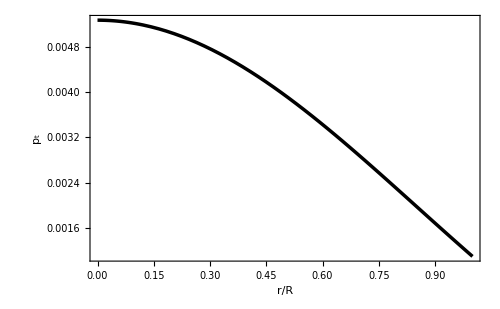

```mathematica
solu1:=Re[Ptg[x]]/.{u->0.17642618727114115}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","p_t"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
ρ[r]/.{M-> u R, r->x R}//FullSimplify
```

(0.0795775 (-0.9-4.76213 √(1-2. u))^(2/3) u (1.35-14.2864 √(1-2. u)-2.25 x^2))/((0.45-4.76213 √(1-2. u)-1.35 x^2)^(5/3))

```mathematica
ρg[x_]:=(0.07957747154594767 (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (1.3499999999999999-14.286394828777734 √(1-2. u)-2.25 x^2))/(0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(5/3)
```

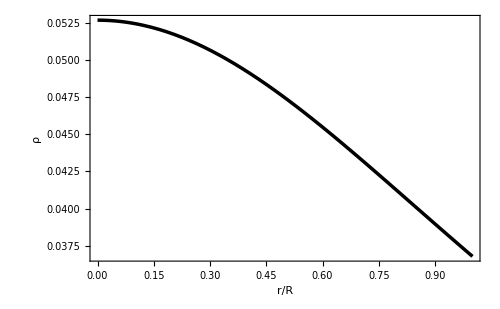

```mathematica
solu1:=Re[ρg[x]]/.{u->0.17642618727114115}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ρ"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

### Gráficas de componentes métricas del espacio-tiempo

```mathematica
Exp[νnumer[r]]/.{M->u R,r->x R}//FullSimplify
```

1. (0.0944955-1. √(1-2. u)-0.0944955 x^2)^2

```mathematica
metric1[x_]:=1. (0.09449549842208152-1. √(1-2. u)-0.09449549842208152 x^2)^2
```

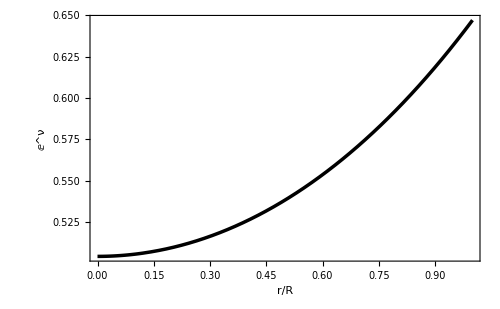

```mathematica
solu1:=Re[metric1[x]]/.{u->0.17642618727114115}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ⅇ^ν"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
Exp[-λ[r]]/.{M-> u R, r->x R}//FullSimplify
```

1-(2. (-0.9-4.76213 √(1-2. u))^(2/3) u x^2)/((0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3))

```mathematica
metric2[x_]:=1-(2. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u x^2)/((0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3))
```

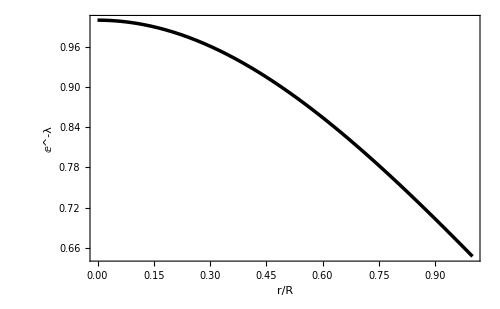

```mathematica
solu1:=Re[metric2[x]]/.{u->0.17642618727114115}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ⅇ^-λ"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

### Condiciones de energía

#### Condición de energía dominante

```mathematica
dec1[x_]:=ρg[x]-Prg[x];
```

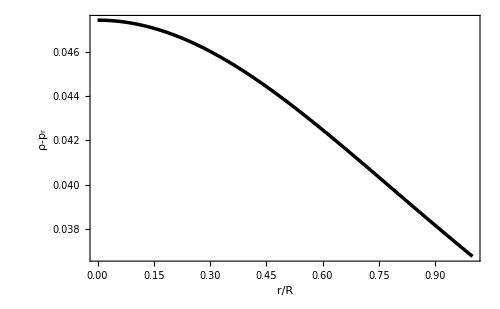

```mathematica
solu1:=Re[dec1[x]]/.{u->0.17642618727114115}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ρ-p_r"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
dec2[x_]:=ρg[x]-Ptg[x];
```

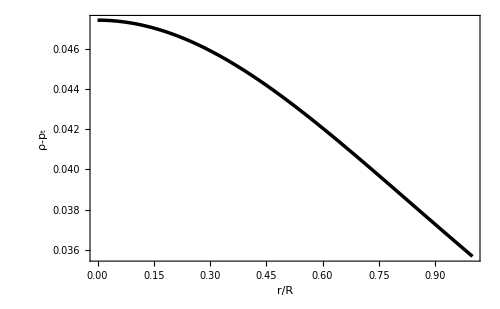

```mathematica
solu1:=Re[dec2[x]]/.{u->0.17642618727114115}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ρ-p_t"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

#### Condicion de energía fuerte

```mathematica
sec[x_]:=ρg[x]-Prg[x]-2*Ptg[x];
```

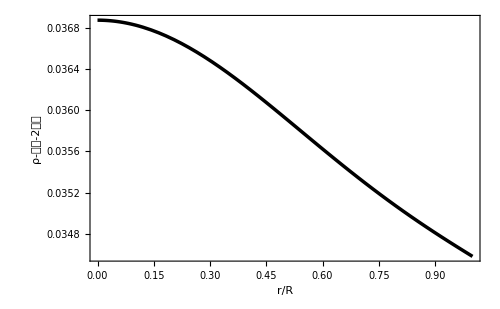

```mathematica
solu1:=Re[sec[x]]/.{u->0.17642618727114115}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","ρ-𝓅𝓇-2𝓅𝓉"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

### Corrimiento al rojo

```mathematica
Z[r_]:=1/(√(ⅇ^(νnumer[r])))-1
```

```mathematica
Z[r]/.{M-> u R, r->x R}//FullSimplify
```

-1+1./(√((0.0944955-1. √(1-2. u)-0.0944955 x^2)^2))

```mathematica
Z[x_]:=-1+1./(√((0.09449549842208152-1. √(1-2. u)-0.09449549842208152 x^2)^2))
```

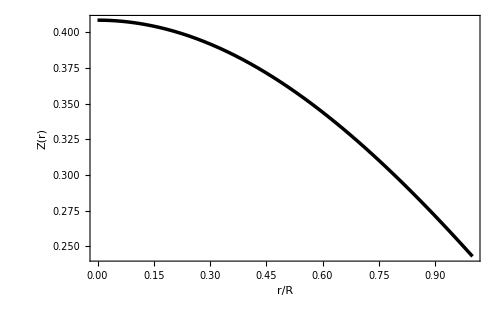

```mathematica
solu1:=Re[Z[x]]/.{u->0.17642618727114115}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","Z(r)"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

### Condición de causalidad:?

#### Velocidad Radial?

```mathematica
vr[r_]:=D[Pr[r],r]/D[ρ[r],r]
vr[r]/.{M-> u R, r->x R}//FullSimplify
```

(0.000243055 (0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3) (1/π(0.45-4.76213 √(1-2. u)-1.35 x^2) (0.45-4.76213 √(1-2. u)-0.45 x^2) (4.86+((-0.9-4.76213 √(1-2. u))^(2/3) u (0.733813-7.76559 √(1-2. u)-3.66907 x^2))/((0.45-4.76213 √(1-2. u)-1.35 x^2)^(2/3))+8.15348 (-0.9-4.76213 √(1-2. u))^(2/3) u (0.45-4.76213 √(1-2. u)-1.35 x^2)^(1/3)+0.0000636877 (((-0.9-4.76213 √(1-2. u))^(2/3) u (1.35-14.2864 √(1-2. u)-2.25 x^2))/((0.45-4.76213 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.0944955+1. √(1-2. u)+0.0944955 x^2)-(0.000212292 (((-0.9-4.76213 √(1-2. u))^(2/3) u (1.35-14.2864 √(1-2. u)-2.25 x^2))/((0.45-4.76213 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.0944955+1. √(1-2. u)+0.0944955 x^2) (-0.0944955+1. √(1-2. u)+0.0944955 x^2))/(-0.0944955+1. √(1-2. u)+0.157492 x^2)+0.0000212292 (((-0.9-4.76213 √(1-2. u))^(2/3) u (1.35-14.2864 √(1-2. u)-2.25 x^2))/((0.45-4.76213 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.0944955+1. √(1-2. u)+0.283486 x^2))+0.286479 (0.45-4.76213 √(1-2. u)-1.35 x^2) (-0.81+8.57184 √(1-2. u)+2.43 x^2+0.000112329 (((-0.9-4.76213 √(1-2. u))^(2/3) u (1.35-14.2864 √(1-2. u)-2.25 x^2))/((0.45-4.76213 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.0944955+1. √(1-2. u)+0.0944955 x^2) (-0.0944955+1. √(1-2. u)+0.283486 x^2)+(-0.9-4.76213 √(1-2. u))^(2/3) u (0.45-4.76213 √(1-2. u)-1.35 x^2)^(1/3) (-0.815348+8.62843 √(1-2. u)+4.07674 x^2))+0.859437 (0.45-4.76213 √(1-2. u)-0.45 x^2) (-0.81+8.57184 √(1-2. u)+2.43 x^2+0.000112329 (((-0.9-4.76213 √(1-2. u))^(2/3) u (1.35-14.2864 √(1-2. u)-2.25 x^2))/((0.45-4.76213 √(1-2. u)-1.35 x^2)^(5/3)))^3. (-0.0944955+1. √(1-2. u)+0.0944955 x^2) (-0.0944955+1. √(1-2. u)+0.283486 x^2)+(-0.9-4.76213 √(1-2. u))^(2/3) u (0.45-4.76213 √(1-2. u)-1.35 x^2)^(1/3) (-0.815348+8.62843 √(1-2. u)+4.07674 x^2))))/((-0.9-4.76213 √(1-2. u))^(2/3) u (0.0944955-1. √(1-2. u)-0.0944955 x^2)^2 (0.0142116-0.150394 √(1-2. u)-0.0142116 x^2))

```mathematica
vr[x_]:= (0.00024305493207293365 (0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3) (1/π(0.45-4.762131609592578 √(1-2. u)-1.35 x^2) (0.45-4.762131609592578 √(1-2. u)-0.45 x^2) (4.86+((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (0.7338133015891135-7.765590042304464 √(1-2. u)-3.6690665079455673 x^2))/(0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(2/3)+8.153481128767927 (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(1/3)+0.00006368771795390506 (((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (1.3499999999999999-14.286394828777734 √(1-2. u)-2.25 x^2))/(0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 x^2)-(0.0002122923931796836 (((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (1.3499999999999999-14.286394828777734 √(1-2. u)-2.25 x^2))/(0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 x^2) (-0.0944954984220815+1. √(1-2. u)+0.09449549842208155 x^2))/(-0.09449549842208152+1. √(1-2. u)+0.15749249737013588 x^2)+0.000021229239317968355 (((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (1.3499999999999999-14.286394828777734 √(1-2. u)-2.25 x^2))/(0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.09449549842208152+1. √(1-2. u)+0.2834864952662446 x^2))+0.2864788975654116 (0.45-4.762131609592578 √(1-2. u)-1.35 x^2) (-0.81+8.571836897266643 √(1-2. u)+2.43 x^2+0.00011232936844855853 (((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (1.3499999999999999-14.286394828777734 √(1-2. u)-2.25 x^2))/(0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 x^2) (-0.09449549842208152+1. √(1-2. u)+0.2834864952662446 x^2)+(-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(1/3) (-0.8153481128767929+8.628433380338295 √(1-2. u)+4.0767405643839645 x^2))+0.8594366926962349 (0.45-4.762131609592578 √(1-2. u)-0.45 x^2) (-0.81+8.571836897266643 √(1-2. u)+2.43 x^2+0.00011232936844855853 (((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (1.3499999999999999-14.286394828777734 √(1-2. u)-2.25 x^2))/(0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(5/3))^3. (-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 x^2) (-0.09449549842208152+1. √(1-2. u)+0.2834864952662446 x^2)+(-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (0.45-4.762131609592578 √(1-2. u)-1.35 x^2)^(1/3) (-0.8153481128767929+8.628433380338295 √(1-2. u)+4.0767405643839645 x^2))))/((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (0.09449549842208152-1. √(1-2. u)-0.09449549842208152 x^2)^2 (0.014211580250282107-0.15039425673806672 √(1-2. u)-0.01421158025028211 x^2))
```

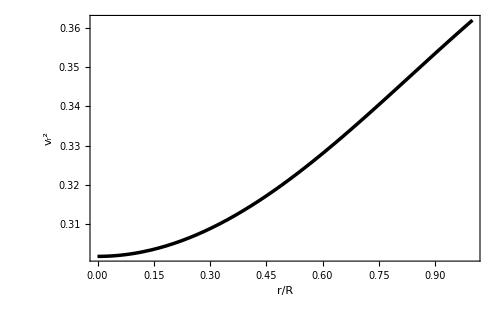

```mathematica
solu1:=vr[x]/.{u->0.17642618727114115}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","v_r^2"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

#### Velocidad Tangencial

```mathematica
vt[r_]:=D[Pt[r],r]/D[ρ[r],r]
vt[r]/.{M-> u R, r->x R}
```

(-(0.0397887 (1-(2. 2 x^2)/1^1) (1-1) (1))/(x (1-1)^2 (1)^2 (-2. 1 u x^2+1)^3)+5+1/1)/((0.358099 3 (9.64689×10^-7 (1.39941×10^6-1)-2.25 x^2))/((3.21563×10^-7 1-1)^(8/3))-(0.358099 111 x)/(1)^(5/3))
 |  |  |  |

```mathematica
vt[x_]:={{(-(0.039788735772973836 (1-(2. 2 x^2)/1^1) (1-1) (1))/(x (1-1)^2 (1)^2 (-2. 1 u x^2+1)^3)+5+1/1)/((0.3580986219567646 3 (9.646888508658564*^-7 (1.39941495*^6-1)-2.25 x^2))/((3.2156295028861884*^-7 1-1)^(8/3))-(0.3580986219567645 1 1 1 x)/(1)^(5/3))}, {{{, , , , }}}}
```

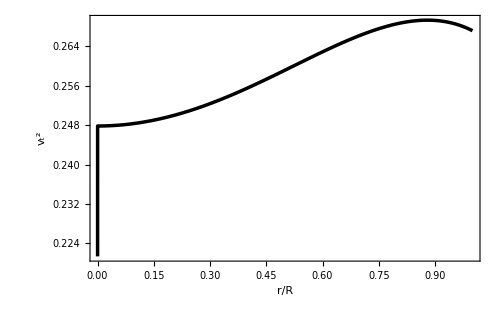

```mathematica
solu1:=Re[vt[x]]/.{u->0.17642618727114115}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","v_t^2"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

## Anisotropía

```mathematica
Π[x_]:=Ptg[x]-Prg[x]
```

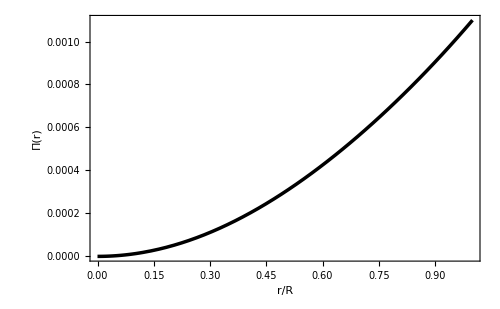

```mathematica
solu1:=Re[Π[x]]/.{u->0.17642618727114115}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","Π(r)"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
Π[x]/.{x->√(x^2+y^2)}//Simplify
```

-((0.00175452 (-0.81+8.57184 √(1-2. u)+2.43 (x^2+y^2)+0.000112329 (((-0.9-4.76213 √(1-2. u))^(2/3) u (1.35-14.2864 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (-0.0944955+1. √(1-2. u)+0.0944955 (x^2+y^2)) (-0.0944955+1. √(1-2. u)+0.283486 (x^2+y^2))+(-0.9-4.76213 √(1-2. u))^(2/3) u (0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(1/3) (-0.815348+8.62843 √(1-2. u)+4.07674 (x^2+y^2))))/((-0.0944955+1. √(1-2. u)+0.0944955 (x^2+y^2)) (-0.0944955+1. √(1-2. u)+0.283486 (x^2+y^2))))+(9.67085×10^-6 (1-(2. (-0.9-4.76213 √(1-2. u))^(2/3) u (x^2+y^2))/((0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(2/3))) (-146.953 (x^2+y^2) (0.0944955-1. √(1-2. u)-0.283486 (x^2+y^2))^2 (1. (-0.9-4.76213 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2+777.565 (0.0944955-1. √(1-2. u)-0.283486 (x^2+y^2))^2 (-0.0944955+1. √(1-2. u)+0.0944955 (x^2+y^2)) (1. (-0.9-4.76213 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2+0.338608 (-0.9-4.76213 √(1-2. u))^(2/3) u (x^2+y^2) (-2. (-0.9-4.76213 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (-107.995 (-0.0944955+1. √(1-2. u))^3-91.8455 (0.0944955-1. √(1-2. u))^2 (x^2+y^2)-22.1796 (-0.0944955+1. √(1-2. u)) (x^2+y^2)^2-1.36688 (x^2+y^2)^3+215.99 (-0.0944955+1. √(1-2. u)) (0.0944955-1. √(1-2. u)-0.283486 (x^2+y^2))^2-0.0426542 (((-0.9-4.76213 √(1-2. u))^(2/3) u (1.35-14.2864 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^2. (-0.0944955+1. √(1-2. u)+0.0944955 (x^2+y^2))^3)+0.5 (x^2+y^2) (0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^2 (3.6 (-0.9-4.76213 √(1-2. u))^(2/3) u (x^2+y^2)-1.8 (0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(2/3)-0.000023588 (((-0.9-4.76213 √(1-2. u))^(2/3) u (1.35-14.2864 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.0944955+1. √(1-2. u)+0.0944955 (x^2+y^2))-0.89583 (-0.9-4.76213 √(1-2. u))^(2/3) u (-0.0944955+1. √(1-2. u)+0.472477 (x^2+y^2)))^2-4. (-0.9-4.76213 √(1-2. u))^(2/3) u (x^2+y^2) (0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2)) (0.45-4.76213 √(1-2. u)-0.45 (x^2+y^2))^2 (0.000023588 (((-0.9-4.76213 √(1-2. u))^(2/3) u (1.35-14.2864 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.0944955+1. √(1-2. u)+0.0944955 (x^2+y^2))+0.89583 (-0.9-4.76213 √(1-2. u))^(2/3) u (-0.0944955+1. √(1-2. u)+0.472477 (x^2+y^2)))-1. (0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^2 (0.45-4.76213 √(1-2. u)-0.45 (x^2+y^2)) (-2. (-0.9-4.76213 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (0.000023588 (((-0.9-4.76213 √(1-2. u))^(2/3) u (1.35-14.2864 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.0944955+1. √(1-2. u)+0.0944955 (x^2+y^2))+0.89583 (-0.9-4.76213 √(1-2. u))^(2/3) u (-0.0944955+1. √(1-2. u)+0.472477 (x^2+y^2)))+2. (-0.9-4.76213 √(1-2. u))^(2/3) u (x^2+y^2) (0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2)) (0.45-4.76213 √(1-2. u)-0.45 (x^2+y^2))^2 (-3.6 (-0.9-4.76213 √(1-2. u))^(2/3) u (x^2+y^2)+1.8 (0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(2/3)+0.000023588 (((-0.9-4.76213 √(1-2. u))^(2/3) u (1.35-14.2864 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.0944955+1. √(1-2. u)+0.0944955 (x^2+y^2))+0.89583 (-0.9-4.76213 √(1-2. u))^(2/3) u (-0.0944955+1. √(1-2. u)+0.472477 (x^2+y^2)))-1. (0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2)) (0.45-4.76213 √(1-2. u)-0.45 (x^2+y^2)) (-2. (-0.9-4.76213 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (90.7116 (-0.9-4.76213 √(1-2. u))^(2/3) u (0.0944955-1. √(1-2. u)-0.0944955 (x^2+y^2))^2+17.1437 (-0.0944955+1. √(1-2. u)+0.283486 (x^2+y^2)) (1. (-0.9-4.76213 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(2/3))+(0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2)) (0.000023588 (((-0.9-4.76213 √(1-2. u))^(2/3) u (1.35-14.2864 √(1-2. u)-2.25 (x^2+y^2)))/((0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(5/3)))^3. (0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.0944955+1. √(1-2. u)+0.0944955 (x^2+y^2))+0.89583 (-0.9-4.76213 √(1-2. u))^(2/3) u (-0.0944955+1. √(1-2. u)+0.472477 (x^2+y^2))))))/((0.0944955-1. √(1-2. u)-0.283486 (x^2+y^2))^2 (0.0944955-1. √(1-2. u)-0.0944955 (x^2+y^2))^2 (1. (-0.9-4.76213 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-4.76213 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2)

```mathematica
Π[x_,y_]:=-((0.0017545160802817416 (-0.81+8.571836897266643 √(1-2. u)+2.43 (x^2+y^2)+0.00011232936844855853 (((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (1.3499999999999999-14.286394828777734 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^3. (-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 (x^2+y^2)) (-0.09449549842208152+1. √(1-2. u)+0.2834864952662446 (x^2+y^2))+(-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(1/3) (-0.8153481128767929+8.628433380338295 √(1-2. u)+4.0767405643839645 (x^2+y^2))))/((-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 (x^2+y^2)) (-0.09449549842208152+1. √(1-2. u)+0.2834864952662446 (x^2+y^2))))+(9.670848470568061*^-6 (1-(2. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (x^2+y^2))/((0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(2/3))) (-146.95277558668357 (x^2+y^2) (0.09449549842208152-1. √(1-2. u)-0.2834864952662446 (x^2+y^2))^2 (1. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2+777.5649530430114 (0.09449549842208152-1. √(1-2. u)-0.2834864952662446 (x^2+y^2))^2 (-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 (x^2+y^2)) (1. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2+0.338607548492829 (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (x^2+y^2) (-2. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (-107.99513236708495 (-0.09449549842208152+1. √(1-2. u))^3-91.84548474167725 (0.09449549842208152-1. √(1-2. u))^2 (x^2+y^2)-22.179627971677437 (-0.09449549842208152+1. √(1-2. u)) (x^2+y^2)^2-1.366875 (x^2+y^2)^3+215.9902647341699 (-0.09449549842208152+1. √(1-2. u)) (0.09449549842208152-1. √(1-2. u)-0.2834864952662446 (x^2+y^2))^2-0.04265420378546604 (((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (1.3499999999999999-14.286394828777734 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^2. (-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 (x^2+y^2))^3)+0.5 (x^2+y^2) (0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^2 (3.6 (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (x^2+y^2)-1.8 (0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(2/3)-0.000023588043686631503 (((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (1.3499999999999999-14.286394828777734 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^3. (0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 (x^2+y^2))-0.8958298388468625 (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (-0.09449549842208152+1. √(1-2. u)+0.47247749211040757 (x^2+y^2)))^2-4. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (x^2+y^2) (0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2)) (0.45-4.762131609592578 √(1-2. u)-0.45 (x^2+y^2))^2 (0.000023588043686631503 (((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (1.3499999999999999-14.286394828777734 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^3. (0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 (x^2+y^2))+0.8958298388468625 (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (-0.09449549842208152+1. √(1-2. u)+0.47247749211040757 (x^2+y^2)))-1. (0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^2 (0.45-4.762131609592578 √(1-2. u)-0.45 (x^2+y^2)) (-2. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (0.000023588043686631503 (((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (1.3499999999999999-14.286394828777734 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^3. (0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 (x^2+y^2))+0.8958298388468625 (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (-0.09449549842208152+1. √(1-2. u)+0.47247749211040757 (x^2+y^2)))+2. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (x^2+y^2) (0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2)) (0.45-4.762131609592578 √(1-2. u)-0.45 (x^2+y^2))^2 (-3.6 (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (x^2+y^2)+1.8 (0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(2/3)+0.000023588043686631503 (((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (1.3499999999999999-14.286394828777734 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^3. (0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 (x^2+y^2))+0.8958298388468625 (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (-0.09449549842208152+1. √(1-2. u)+0.47247749211040757 (x^2+y^2)))-1. (0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2)) (0.45-4.762131609592578 √(1-2. u)-0.45 (x^2+y^2)) (-2. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (x^2+y^2)+(0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(2/3)) (90.7115898683232 (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (0.09449549842208152-1. √(1-2. u)-0.09449549842208152 (x^2+y^2))^2+17.14367379453328 (-0.09449549842208152+1. √(1-2. u)+0.2834864952662446 (x^2+y^2)) (1. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(2/3))+(0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2)) (0.000023588043686631503 (((-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (1.3499999999999999-14.286394828777734 √(1-2. u)-2.25 (x^2+y^2)))/(0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(5/3))^3. (0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(2/3) (-0.09449549842208152+1. √(1-2. u)+0.09449549842208152 (x^2+y^2))+0.8958298388468625 (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (-0.09449549842208152+1. √(1-2. u)+0.47247749211040757 (x^2+y^2))))))/((0.09449549842208152-1. √(1-2. u)-0.2834864952662446 (x^2+y^2))^2 (0.09449549842208152-1. √(1-2. u)-0.09449549842208152 (x^2+y^2))^2 (1. (-0.9000000000000001-4.762131609592578 √(1-2. u))^(2/3) u (x^2+y^2)-0.5 (0.45-4.762131609592578 √(1-2. u)-1.35 (x^2+y^2))^(2/3))^2)
```

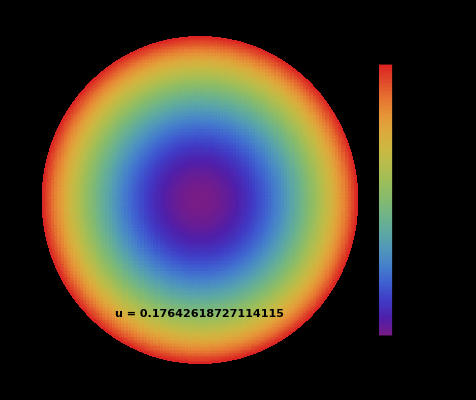

```mathematica
DensityPlot[Re[Π[x,y]]/.{u->0.17642618727114115},{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},0<x^2+y^2<1],ColorFunction->"Rainbow",MeshStyle->Opacity[0.1,Black],PlotLegends->Automatic,Background->Black,Frame->False,Epilog->Text[Style["u = 0.17642618727114115",Large,Bold],{0,-0.7}],PlotPoints->100]
```

## Cracking Gravitacional?

### Falta actualizar desede aqui para abajo, pero no cumple por lo visto en la vt^2

```mathematica
CG[x_]:=vt[x]-vr[x]
```

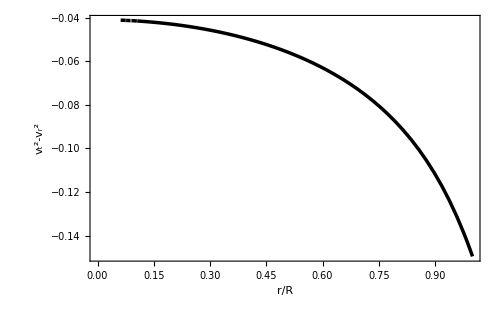

```mathematica
solu1:=CG[x]/.{u->0.302917356305}
Plot[{solu1},{x,0,1},Evaluated->True,PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.005]
},{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Pink,Thickness[0.005]}},Frame->True,FrameLabel->{"r/R","v_t^2-v_r^2"},ImageSize->500,LabelStyle->{FontSize->23,FontFamily->"Times",Black},PlotRange->Automatic]
```

```mathematica
CG[x]/.{x->√(x^2+y^2)}
```

-((0.00472044 1 (1/π(0.45-2.26846 √(1-2. u)-1.35 (x^2+y^2)) 1 (4.86+1/1+1+1-1/1+5.50302×10^-6 (1/1)^3. (-0.198372+1. √(1-2. u)+0.595116 (x^2+y^2)))+1+0.859437 (0.45-1-0.45 (1)) (-0.81+3+(-0.9-2.26846 √(1-2. u))^(2/3) u (0.45-1-1)^(1/3) (-0.829352+4.18079 √(1-2. u)+4.14676 (x^2+y^2)))))/((-0.9-2.26846 √(1-2. u))^(2/3) u (0.198372-1. √(1-2. u)-0.198372 (x^2+y^2))^2 (0.0626299-0.315719 √(1-2. u)-0.0626299 (x^2+y^2))))-(0.000917315 (0.45-2.26846 1-1.35 (x^2+y^2))^(2/3) (1)^2 (7+1))/((-0.9-2.26846 √(1-1))^(2/3) u √(x^2+y^2) (20-1-1) (1)^3 (1)^3 (1. 1 u (x^2+y^2)-0.5 1)^3)
 |  |  |  |

```mathematica
CG2d[x_,y_]:={{-((0.004720439574565849 1 (1/π(0.45-2.2684640056268837 √(1-2. u)-1.35 (x^2+y^2)) 1 (4.86+1/1+1+1-1/1+5.503022504604416*^-6 (1/1)^3. (-0.1983721138549182+1. √(1-2. u)+0.5951163415647547 (x^2+y^2)))+1+0.8594366926962349 (0.45-1-0.45 (1)) (-0.81+3+(-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (0.45-1-1)^(1/3) (-0.8293524416135881+4.180791470620436 √(1-2. u)+4.1467622080679405 (x^2+y^2)))))/((-0.9000000000000001-2.2684640056268837 √(1-2. u))^(2/3) u (0.1983721138549182-1. √(1-2. u)-0.1983721138549182 (x^2+y^2))^2 (0.06262985035679756-0.3157190249159851 √(1-2. u)-0.06262985035679754 (x^2+y^2))))-(0.0009173153429009489 (0.45-2.2684640056268837 1-1.35 (x^2+y^2))^(2/3) (1)^2 (7+1))/((-0.9000000000000001-2.2684640056268837 √(1-1))^(2/3) u √(x^2+y^2) (20-1-1) (1)^3 (1)^3 (1. 1 u (x^2+y^2)-0.5 1)^3)}, {{{, , , , }}}}
```

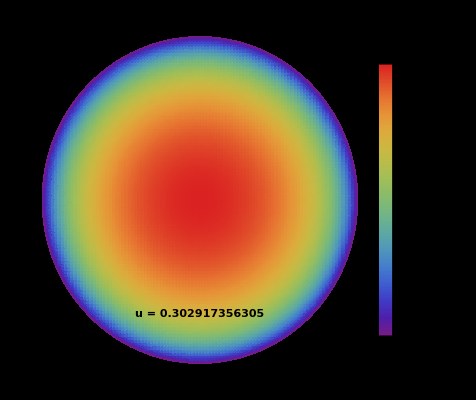

```mathematica
DensityPlot[Re[CG2d[x,y]]/.{u->0.302917356305},{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},0<x^2+y^2<1],ColorFunction->"Rainbow",MeshStyle->Opacity[0.1,Black],PlotLegends->Automatic,Background->Black,Frame->False,Epilog->Text[Style["u = 0.302917356305",Large,Bold],{0,-0.7}],PlotPoints->100]
```